```mathematica
?Module
```

```mathematica
complcatedFunction[x_]:= Sin[1 + Exp[x] π - x/2];
```

```mathematica
complcatedFunction1[x_]:= Module[{a , b , c = 1},
a = 1 + Exp[x] π;
b = - x/2;
Print[c];
Sin[a + b]
]
```

```mathematica
complcatedFunction[1.]
```

0.3756

```mathematica
{a , b} = {2 , 3};
```

```mathematica
complcatedFunction1[1.]
```

1

0.3756

```mathematica
a
```

2

```mathematica
b
```

3

```mathematica
Hold[FullForm[
Module[{a , b , c = 1},
a = 1 + Exp[x] π;
b = - x/2;
Print[c];
Sin[a + b]
]
]]
```

Hold[Module[List[a,b,Set[c,1]],CompoundExpression[Set[a,Plus[1,Times[Exp[x],Pi]]],Set[b,Times[-1,Times[x,Power[2,-1]]]],Print[c],Sin[Plus[a,b]]]]]

```mathematica
xx = 123;
yy = 321;
xx + Sin[yy]
```

123+Sin[321]

```mathematica
Hold[FullForm[
xx = 123;
yy = 321;
xx + Sin[yy]
]]
```

Hold[CompoundExpression[Set[xx,123],Set[yy,321],Plus[xx,Sin[yy]]]]

```mathematica
?For
```

```mathematica
For[i = 1 , i <= 5 , i = i + 1 , 
Print[i]
];
```

1

2

3

4

5

```mathematica
Do[Print[{i , j}] , {i , 1 , 50 , 10} ,{j , 1 , 2}]
```

{1,1}

{1,2}

{11,1}

{11,2}

{21,1}

{21,2}

{31,1}

{31,2}

{41,1}

{41,2}

```mathematica
?TableForm
```

```mathematica
TableForm[Table[i j , {i , 1 , 50, 10} , {j , 1 , 2}] , TableHeadings->{{1 , 2 , 3 , 4 ,5} , {"column 1" , "column 2"}}]//TeXForm
```

\begin{array}{c|c|c}
  & \text{column 1} & \text{column 2} \\
\hline
 1 & 1 & 2 \\
\hline
 2 & 11 & 22 \\
 3 & 21 & 42 \\
 4 & 31 & 62 \\
 5 & 41 & 82 \\
\end{array}

```mathematica
MatrixForm[Table[i j , {i , 1 , 50, 10} , {j , 1 , 2}]]
```

(1 | 2
11 | 22
21 | 42
31 | 62
41 | 82)

```mathematica
?OptionsPattern
```

```mathematica
f[x_ , OptionsPattern["y" -> 1]]:= x OptionValue["y"];
```

```mathematica
f[2]
```

2

```mathematica
f[1 , "y" -> 123]
```

123

```mathematica
g[x_ , OptionsPattern[{"y" -> 1 , "z" -> 1}]]:= x OptionValue["y"] OptionValue["z"];
```

```mathematica
g[2 , "y"-> 2 , "z"-> 2]
```

8

```mathematica
g[2 , "z"-> 2 , "y"-> 2]
```

8

```mathematica
g[2 , "z"-> 2]
```

4

```mathematica
g[2]
```

2

```mathematica
y::usage = "Optional argument to h";
z::usage = "Optional argument to h";
```

```mathematica
?y
```

```mathematica
?z
```

```mathematica
h[x_ , OptionsPattern[{y -> 1 , z -> 1}]]:= x OptionValue[y] OptionValue[z];
```

```mathematica
h[2 , y-> 123 , z-> 321]
```

78966

```mathematica
Clear[hh]
```

```mathematica
hh[OptionsPattern[{"1"-> 2}]]:= OptionValue["1"];
```

```mathematica
hh[]
```

2

```mathematica
Options[gg] = {"1"-> 2};
```

```mathematica
gg[OptionsPattern[]]:=OptionValue["1"];
```

```mathematica
gg[]
```

2

```mathematica
line = lineData[p1:{_ , _} , p2:{_ , _}]/;p1 != p2;
firstPoint[l : line]:= l[[1]];
secondPoint[l : line]:= l[[2]];
```

```mathematica
getPointOnLine[l: line]:= Function[t , firstPoint[l] + t Normalize[secondPoint[l] - firstPoint[l]]];
```

```mathematica
ffff = getPointOnLine[lineData[{0 , 0} , {1 , 1}]];
```

```mathematica
ffff[1]
```

{1/(√2),1/(√2)}

```mathematica
Clear[draw]
```

```mathematica
draw[l : line]:= Graphics[InfiniteLine[{firstPoint[l] , secondPoint[l]}] , PlotRange->{{-2 , 2} , {-2 , 2}} , Frame->True];
```

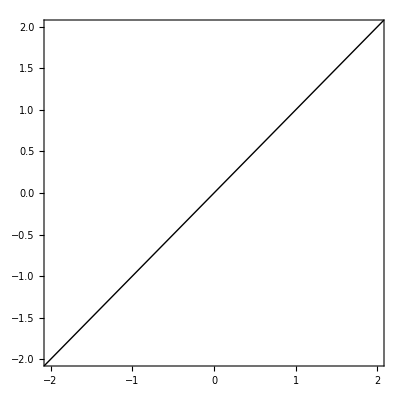

```mathematica
draw[lineData[{0 , 0} , {2 , 2}]]
```

```mathematica
Hold[FullForm[
draw[l : line]
]]
```

Hold[draw[Pattern[l,line]]]

```mathematica
{1 , 2 , 3}//Norm
```

√14

```mathematica
Normalize[{1 , 2 ,3}]
```

{1/(√14),√(2/7),3/(√14)}

```mathematica
%//Norm//N
```

1.

```mathematica
Cross[{0 , 0 , 1} , {0 , 1 , 0}]
```

{-1,0,0}

```mathematica
Table[
Sum[
LeviCivitaTensor[3][[i , j , k]]{0 , 0 , 1}[[j]] {0 , 1 , 0}[[k]] , 
{j , 1 , 3} , {k , 1 , 3}] , {i , 1 , 3}]
```

{-1,0,0}

```mathematica
(#)&[1]
```

1

```mathematica
(#1 + #2)&[1 , 2]
```

3

```mathematica
Hold[FullForm[(#1 + #2)&[1 , 2]]]
```

Hold[Function[Plus[Slot[1],Slot[2]]][1,2]]

```mathematica
Function[{x , y} , x + y][1 , 2]
```

3

```mathematica
(*|->*)
```

```mathematica
(x|->2 x)[3]
```

6

```mathematica
({x , y}|->2 x+ y)[3 , 2]
```

8

```mathematica
fff[x_]:= (y|-> y + x);
```

```mathematica
addTwo = fff[2];
```

```mathematica
addTwo[123]
```

125

```mathematica
addTwo[100]
```

102

```mathematica
plus[x_][y_]:=x + y;
```

```mathematica
addTwoB = plus[2];
```

```mathematica
addTwoB[123]
```

125

```mathematica
addTwo[100]
```

102

```mathematica
?Orthogonalize
```

```mathematica
Orthogonalize[{
{1 , 0 , 0},
{1 , 1 , 0}
}]
```

{{1,0,0},{0,1,0}}

```mathematica
?Throw
```

```mathematica
Clear[asdf]
```

```mathematica
asdf[x_]:=If[
x <0 , 
Throw["asdf[x] expects a positive real number as x!!!"],
x,
Throw["!@#!#@@!!!!!"]
];
```

```mathematica
asdf[1]
```

1

```mathematica
asdf[-1]
```

Throw::nocatch: Uncaught Throw[asdf[x] expects a positive real number as x!!!] returned to top level.

Hold[Throw[asdf[x] expects a positive real number as x!!!]]